### Start choosing the example:

```mathematica
t=4;
beta=0;
A=0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"]
Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{4,U1}},"Switching Costs"->{}|>;
d2e=Data2Equations[Data/.{I1-> 80, U1-> 0}];
CriticalCongestionSolver[d2e]
```

j1==0&&j10==80&&j2==80&&j3==0&&j4==80&&j5==0&&j6==80&&j7==0&&j8==80&&j9==0&&jt1==0&&jt2==80&&jt3==80&&jt4==0&&jt5==80&&jt6==0&&jt7==80&&jt8==0&&u1==u10&&u1-u10==0&&u2==u3&&-u2+u3==0&&u4==u5&&-u4+u5==0&&-u6==0&&u6==0&&u7==0&&u8==0&&u9==u10

j1==0&&j10==80&&j2==80&&j3==0&&j4==80&&j5==0&&j6==80&&j7==0&&j8==80&&j9==0&&jt1==0&&jt2==80&&jt3==80&&jt4==0&&jt5==80&&jt6==0&&jt7==80&&jt8==0&&u10==u1&&u3==u2&&u5==u4&&u6==0&&u7==0&&u8==0&&u9==u1

Checking (replacing updated rules in both systems)...

Ok!

FinalClean...

NewReduce of Not[Or OR And]: True

<|j10→80,j9→0,j7→0,j2→80,j1→0,j4→80,j3→0,j6→80,j5→0,j8→80,u8→0,jt1→0,jt2→80,jt3→80,jt4→0,jt5→80,jt6→0,jt7→80,jt8→0,u7→0,u9→240,u10→240,u3→160,u5→80,u6→0,u1→240,u2→160,u4→80|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 80, U1-> 15}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.060172,<|u1→255,u2→175,u3→175,u4→95,u5→95,u6→15,u7→15,u8→15,u9→255,u10→255,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

Finished with the us!

Done!

{0.004322,<|u1→255,u2→175,u3→175,u4→95,u5→95,u6→15,u7→15,u8→15,u9→255,u10→255,j1→0,j2→80,j3→0,j4→80,j5→0,j6→80,j7→0,j8→80,j9→0,j10→80|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.010141,Null}

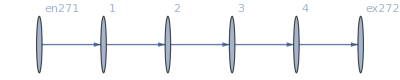

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j273→80.,j274→80.,j275→80.,j276→80.,j277→80.,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80.,jt285→80.,jt286→0.,jt287→80.,jt288→0.,jt289→80.,jt290→0.,u291→255.,u292→175.,u293→95.,u294→15.,u295→255.,u296→175.,u297→95.,u298→15.,u299→15.,u300→255.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→22.7459,u292→20.1639,u293→17.582,u294→15.,u295→22.7459,u296→20.1639,u297→17.582,u298→15.,u299→15.,u300→22.7459|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→24.484,u292→21.3227,u293→18.1613,u294→15.,u295→24.484,u296→21.3227,u297→18.1613,u298→15.,u299→15.,u300→24.484|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→30.0717,u292→25.0478,u293→20.0239,u294→15.,u295→30.0717,u296→25.0478,u297→20.0239,u298→15.,u299→15.,u300→30.0717|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.47684×10^-13,ComplexInfinity]

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→255.,u292→175.,u293→95.,u294→15.,u295→255.,u296→175.,u297→95.,u298→15.,u299→15.,u300→255.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.00219×10^-16

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→1106.72,u292→742.811,u293→378.906,u294→15.,u295→1106.72,u296→742.811,u297→378.906,u298→15.,u299→15.,u300→1106.72|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→870144.,u292→580101.,u293→290058.,u294→15.,u295→870144.,u296→580101.,u297→290058.,u298→15.,u299→15.,u300→870144.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.37917×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.37917×10^-16

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→4.6785×10^7,u292→3.119×10^7,u293→1.5595×10^7,u294→15.,u295→4.6785×10^7,u296→3.119×10^7,u297→1.5595×10^7,u298→15.,u299→15.,u300→4.6785×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.83133×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.83133×10^-16

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→7.21578×10^10,u292→4.81052×10^10,u293→2.40526×10^10,u294→15.,u295→7.21578×10^10,u296→4.81052×10^10,u297→2.40526×10^10,u298→15.,u299→15.,u300→7.21578×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.82736×10^-16

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→1.68111×10^19,u292→1.12074×10^19,u293→5.6037×10^18,u294→15.,u295→1.68111×10^19,u296→1.12074×10^19,u297→5.6037×10^18,u298→15.,u299→15.,u300→1.68111×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.84774×10^-16

<|j273→80,j274→80,j275→80,j276→80,j277→80,j278→0.,j279→0.,j280→0.,j281→0.,j282→0.,jt283→0.,jt284→80,jt285→80,jt286→0.,jt287→80,jt288→0.,jt289→80,jt290→0.,u291→6.61469×10^106,u292→4.4098×10^106,u293→2.2049×10^106,u294→15.,u295→6.61469×10^106,u296→4.4098×10^106,u297→2.2049×10^106,u298→15.,u299→15.,u300→6.61469×10^106|>